Assignment 3. Question 1.

Define the FLRW Metric

Using κ in the metric instead of k so that I can Sum[] over k later on in the notebook.

```mathematica
metric = {{-1, 0, 0, 0},{0,a[t]^2/(1-κ*r^2),0,0},{0,0,a[t]^2*r^2,0},{0,0,0,a[t]^2*r^2*Sin[θ]^2}};
metric//MatrixForm
```

(-1 | 0 | 0 | 0
0 | a[t]^2/(1-r^2 κ) | 0 | 0
0 | 0 | r^2 a[t]^2 | 0
0 | 0 | 0 | r^2 a[t]^2 Sin[θ]^2)

Evaluate the inverse metric

```mathematica
inversemetric = Simplify[Inverse[metric]];
inversemetric//MatrixForm
```

(-1 | 0 | 0 | 0
0 | (1-r^2 κ)/a[t]^2 | 0 | 0
0 | 0 | 1/(r^2 a[t]^2) | 0
0 | 0 | 0 | Csc[θ]^2/(r^2 a[t]^2))

Calculate the Christoffel connection of the first kind

```mathematica
(*Set up list of coordinates to differentiate with respect to*)
coords = {t,r,θ,ϕ}
```

{t,r,θ,ϕ}

```mathematica
gamma = Simplify[Table[1/2*(D[Part[metric,i,j],coords[[k]]] + D[Part[metric,i,k],coords[[j]]] - D[Part[metric,j,k],coords[[i]]]),
{i,1,4},{j,1,4},{k,1,4}]
];
```

Calculate Christoffel connection of the second kind

```mathematica
secondgamma = Simplify[Table[1/2*Sum[Part[inversemetric,i,n]*(D[Part[metric,n,j],coords[[k]]] + D[Part[metric,n,k],coords[[j]]] - D[Part[metric,j,k],coords[[n]]]),{n,4}],
{i,4},{j,4},{k,4}]
];
```

Calculate the Riemann tensor. This has the first index raised and the final three lowered.

```mathematica
riemann = Simplify[Table[ 
-D[Part[secondgamma,i,j,k],coords[[l]]] + D[Part[secondgamma,i,l,j],coords[[k]]] +
Sum[-Part[secondgamma,i,l,s]*Part[secondgamma,s,j,k] +Part[secondgamma,i,k,s]*Part[secondgamma,s,j,l],{s,1,4}],
{i,1,4},{j,1,4},{k,1,4},{l,1,4}]
];
```

#### Calculate the Ricci tensor.

```mathematica
riccitensor= Simplify[Table[ 
Sum[Part[riemann,i,p,i,s],{i,1,4}],
{p,1,4},{s,1,4}]];
```

#### Print the tt, rr, θθ, and ϕϕ components of the Ricci tensor

```mathematica
Part[riccitensor,1,1]
```

-(3 a''[t])/a[t]

```mathematica
Part[riccitensor,2,2]
```

Part::partd: Part specification riccitensor⟦2,2⟧ is longer than depth of object.

riccitensor⟦2,2⟧

```mathematica
Part[riccitensor,3,3]
```

r^2 (2 (κ+a'[t]^2)+a[t] a''[t])

```mathematica
Part[riccitensor,4,4]
```

r^2 Sin[θ]^2 (2 (κ+a'[t]^2)+a[t] a''[t])

```mathematica
Calculate the Ricci scalar.
```

```mathematica
ricciscalar = Simplify[Sum[Part[inversemetric,i,j]*Part[riccitensor,i,j],{i,1,4},{j,1,4}]]
```

(6 (κ+a'[t]^2+a[t] a''[t]))/a[t]^2

Calculate Gtt

```mathematica
gtt = Simplify[Part[riccitensor,1,1]-1/2*Part[metric,1,1]*ricciscalar]
```

(3 (κ+a'[t]^2))/a[t]^2

### Question 3. Plot dA[z] and δθ[z].

#### Define Einstein-de Sitter angular distance dA[z], and angle in the sky δθ[z].

```mathematica
dAeinstein[z_, c_, Ho_] = -2*c/(Ho*(1+z))*(1/(1+z)^(1/2)-1)
```

-(2 c (-1+1/(√(1+z))))/(Ho (1+z))

```mathematica
δθeinstein[z_, c_, Ho_, d_] = d/dAeinstein[z,c,Ho]
```

-(D Ho (1+z))/(2 c (-1+1/(√(1+z))))

#### Define the parameters

```mathematica
c = 3*10^5(*km/s*)
Ho =70 (*km/s/Mpc*)
d = 1 (*Mpc*)
```

300000

70

1

#### Plot the angular displacement

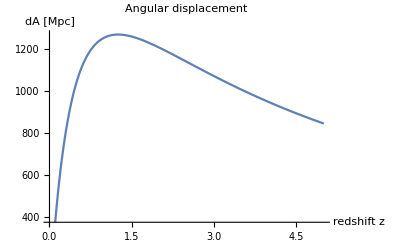

```mathematica
Plot[{dAeinstein[z,c,Ho]},{z,0,5},
PlotLabel->"Angular displacement",
AxesLabel->{"redshift z","dA [Mpc]"}]
```

#### Plot the angle in the sky

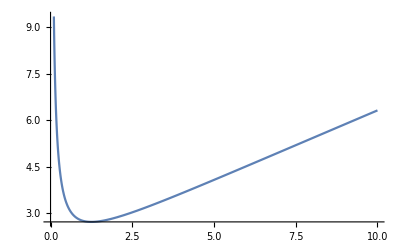

```mathematica
Plot[{δθeinstein[z, c, Ho, d]*180*60/Pi},{z,0,10}]
```